```mathematica
(* Lucy weight function *)
w[r_,h_]:= If[r <h, 5/(9 π) (1+ 3 r/h)(1-(r/h))^3,0]
```

```mathematica
wp[r_,h_]:= If[r <h,D[ 5/(9 π) (1+ 3 r/h)(1-(r/h))^3,r],0]
```

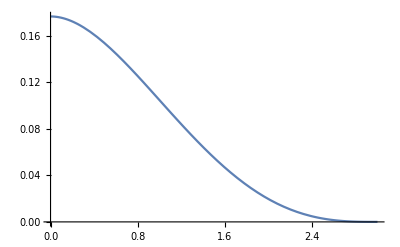

```mathematica
np = Plot[w[r,3],{r,0,3}]
```

```mathematica
wp1 = D[w[r,h],r]/.{h->3}
```

If[r<3,(3 (5 (1-r/3)^3))/(3 (9 π))-((3 (1-r/3)^2) (5 (1+(3 r)/3)))/(3 (9 π)),0]

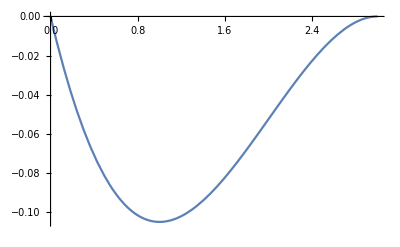

```mathematica
d1 =Plot[wp1 /.r->x,{x,0,3}]
```

```mathematica
wp2 =D[w[r,h]/.{h->3},{r,2}]
```

If[r<3,-(10 (1-r/3)^2)/(9 π)+(10 (1-r/3) (1+r))/(27 π),0]

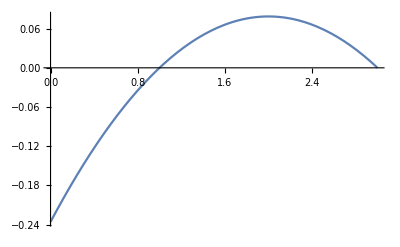

```mathematica
d2 = Plot[wp2/. r->x,{x,0,3}]
```

The function of the weight seems to chosen to have smooth derivatives on the right boundary of the range.
This could be because of jumps in force due to nonsmooth derivatives of the force field.

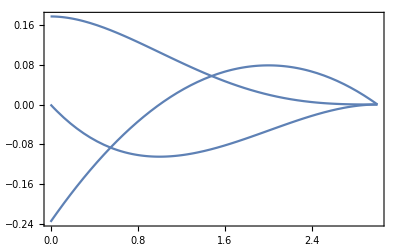

```mathematica
Show[{np,d1,d2},PlotRange->All,Frame->True]
```